## Naloga 3

Sestavite funkcijo zivljenje[svet_], kot je zapisano v navodilih.

```mathematica
zivljenje[svet_]:=
```

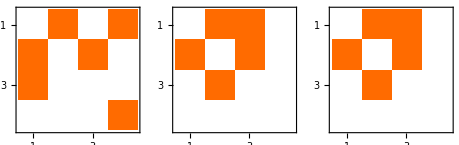

```mathematica
svet1={{0,1,0,1},{1,0,1,0},{1,0,0,0},{0,0,0,1}};
GraphicsRow[MatrixPlot/@{svet1,zivljenje[svet1],zivljenje[zivljenje[svet1]]}]
```

Ugotovite, koliko korakov je potrebno narediti, da svet dieHard izumre.

```mathematica
dieHard={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
Manipulate[MatrixPlot[Nest[zivljenje,svet1,u]],{u,0,100,1}]
```

## Naloga 4

Sestavite funkcijo krogi[l_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
krogi[l_]:=
```

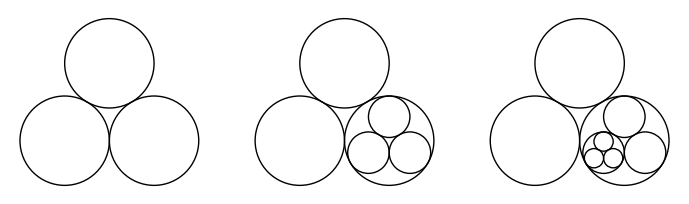

```mathematica
GraphicsRow[{krogi[{}],krogi[{2}],krogi[{2,1}]}]
```